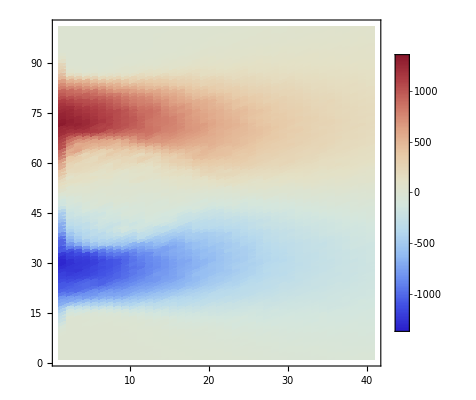

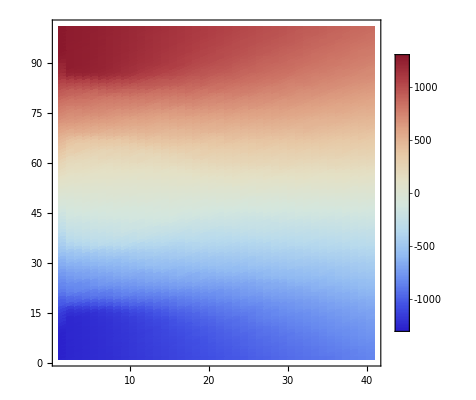

```mathematica
dataSD=Transpose@ToExpression@Import["F:\\Project\\HeisenbergModel\\Debug\\Result_SD_Step=10000_T=0~2_B=-5~5.csv"];
ListDensityPlot[dataSD,PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
dataMz=Transpose@ToExpression@Import["F:\\Project\\HeisenbergModel\\Debug\\Result_Mz_Step=10000_T=0~2_B=-5~5.csv"];
ListDensityPlot[dataMz,PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

```mathematica
absDataSD=Abs[dataSD];
absDataMz=Abs[dataMz];
```

-Graphics-

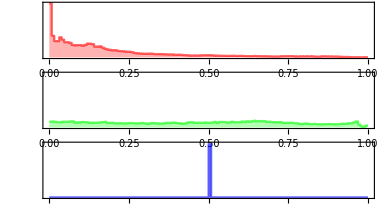

```mathematica
img=ImageResize[#,{400,400}]&@Image[Table[{(#⟦i⟧⟦j⟧-Min[#])/(Max[#]-Min[#])&@absDataSD,(#⟦i⟧⟦j⟧-Min[#])/(Max[#]-Min[#])&@absDataMz,0.5},{i,1,101},{j,1,41}],ColorSpace->"RGB",ImageSize->Small]
ImageHistogram[img,Appearance->"Separated",ImageSize->Medium]
```

```mathematica
ColorNegate@EdgeDetect[img,50]
```

-Graphics-

```mathematica
SetAlphaChannel[img,ColorNegate@EdgeDetect[img,50]]
```

-Graphics-

-Graphics-

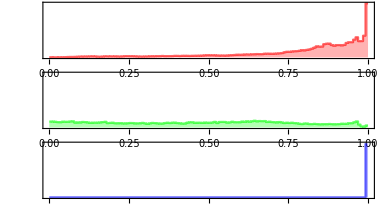

```mathematica
img=ImageResize[#,{400,400}]&@Image[Table[{1-(#⟦i⟧⟦j⟧-Min[#])/(Max[#]-Min[#])&@absDataSD,(#⟦i⟧⟦j⟧-Min[#])/(Max[#]-Min[#])&@absDataMz,1},{i,1,101},{j,1,41}],ColorSpace->"RGB",ImageSize->Small]
ImageHistogram[img,Appearance->"Separated",ImageSize->Medium]
```

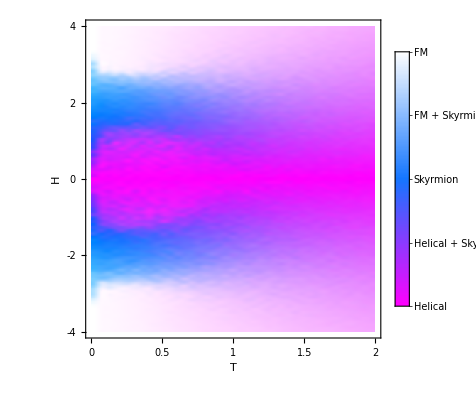

```mathematica
Legended[
Graphics[
Raster[ImageData@img],
Frame->True,FrameLabel->{"T","H"},
FrameTicks->{{Table[{400i/8,i-4},{i,0,8,2}],None},{{{0,0},{100,0.5},{200,1},{300,1.5},{400,2}},None}},
LabelStyle->{FontFamily->"Segoe UI",FontSize->12}
],
BarLegend[{Blend[{RGBColor[{1, 0, 1}],RGBColor[{Rational[4, 51], Rational[118, 255], 1}],RGBColor[{1, 1, 1}]},#]&,{0,1}},Ticks->{{0,"Helical"},{0.25,"Helical + Skyrmion"},{0.5,"Skyrmion"},{0.75,"FM + Skyrmion"},{1,"FM"}},LabelStyle->{FontFamily->"Segoe UI",FontSize->12}]
]
```

```mathematica
rasterizeBackground[g_,res_: 450]:=Show[Rasterize[Show[g,PlotRangePadding->0,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res]/.Raster[data_,rect_,rest__]:>Raster[data,Transpose@OptionValue[AbsoluteOptions[g,PlotRange],PlotRange],rest],Sequence@@Options[g],Sequence@@Options[g,PlotRange]]
```

```mathematica
Legended[rasterizeBackground[
ListDensityPlot[#,
ColorFunction->"ThermometerColors",
FrameLabel->{"T","H"},LabelStyle->{FontFamily->"Segoe UI",FontSize->10},
FrameTicks->{{Table[{100i/8+1,i-4},{i,0,8,2}],None},{{{1,0},{41/4,0.5},{41/2,1},{41/4 3,1.5},{41,2}},None}}
],
100],BarLegend[{"ThermometerColors",{Min[#],Max[#]}/36^2},LabelStyle->{FontFamily->"Segoe UI",FontSize->10},LegendLabel->"Skyrmion\ndensity"]
]&@dataSD
```

-Graphics-

```mathematica
Legended[rasterizeBackground[
ListDensityPlot[#,
ColorFunction->"ThermometerColors",
FrameLabel->{"T","H"},LabelStyle->{FontFamily->"Segoe UI",FontSize->10},
FrameTicks->{{Table[{100i/8+1,i-4},{i,0,8,2}],None},{{{1,0},{41/4,0.5},{41/2,1},{41/4 3,1.5},{41,2}},None}}
],
100],BarLegend[{"ThermometerColors",{Min[#],Max[#]}/36^2},LabelStyle->{FontFamily->"Segoe UI",FontSize->10},LegendLabel->"z component of\nmagnetic dipoles"]
]&@dataMz
```

-Graphics-

```mathematica
-Graphics--Graphics-
```